# Predict the Scale of Satellite Images

Some explanation

Mehmet Sahin, Jun. 26,  2018

Some explanation

```mathematica
Quit
```

## Collect Satellite Images

In this section, we will get the data using GeoImage.

Some explanation

```mathematica
(*ClearAll["Global`*"]*)
```

Create a function to get countries’ geo positions randomly:

```mathematica
geoPositionOfCountry[entities_,numberOfPosition_Integer,folderName_String] :=
	Module[
		{countries, mesh},
		countries = entities;
		mesh = DiscretizeGraphics@EntityValue[countries,"Polygon"];
		SeedRandom[Hash@{folderName,countries}];
		Reverse[RandomPoint[mesh,numberOfPosition],{2}]
	]
```

Let’s plot them and see how those random positions act on a Graphic

```mathematica
(*trainingDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},500,"training"];
validationDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},100,"validation"];
testingDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},25,"testing"];*)

trainingDataOfCities = geoPositionOfCountry[{},850,"training"];
validationDataOfCities = geoPositionOfCountry[{},100,"validation"];
testingDataOfCities = geoPositionOfCountry[{},50,"testing"];

GeoListPlot@GeoPosition@trainingDataOfCountry
GeoListPlot@GeoPosition@trainingDataOfCities
```

Old normaliser function:

```mathematica
(*b = geoPositionOfCountry[{},50,"testing"];
ClearAll[getZoomLevel, getGeoRange]
SetAttributes[getGeoRange, Listable]
(*Rondom point distrubition*)
(*getZoomLevel[point_List,max_] := 
	With[
		{cutoff = 0.05},
		SeedRandom[Hash[point]]; 
		Clip[RandomVariate[HalfNormalDistribution[ If[max≤10,2,5]]],{0,1 - cutoff}] + cutoff
	];*)
getZoomLevel[] := 
	With[
	{random =RandomReal[]},
	If[random<0.1,0.1,random]  (*0.2*)  
	];

randomPoints = getZoomLevel[]& /@ b; 
ListPlot[randomPoints]
Histogram[randomPoints,PlotRange->All]
randomPoints
Count[randomPoints,y_/;y<0.5]

(*getGeoRange[zoom_,max_] := zoom * max; *)
getGeoRange[zoom_,max_] := Round[zoom * max,0.1]; (*no round !*)
getGeoRange[#,10]& /@  randomPoints*)
```

New normaliser function for geo range:

```mathematica
ClearAll[pointRange, rescale]
SetAttributes[{rescale, revertRescale}, Listable]
$minscale = 0.2;
$maxscale = 8000;
function = Function[#^6];
rescale[x_, min_: $minscale, max_: $maxscale] := 
 (x - min) / (max - min)
revertRescale[x_, min_: $minscale, max_: $maxscale] := 
 min + x * (max - min)
pointRange[zmin_, zmax_, length_: 10]  := 
 Table[
  rescale[x], 
  {x, zmin, zmax, (zmax - zmin) / (length - 1)}
  ]
  
test[zmin_, zmax_, length_: 10] := Column[{{
    ListPlot[Map[{#, function[#]} &, pointRange[zmin, zmax, length]], 
     PlotRange -> {{0, 1}, {0, 1}}],
    ListPlot[
     Map[{#, function[#]} &, 
      pointRange[$minscale, $maxscale , length]], 
     PlotRange -> {{0, 1}, {0, 1}}]
    }, {
    Histogram @ Map[function, pointRange[zmin, zmax, length]],
    Histogram @ 
     Map[function, pointRange[$minscale, $maxscale , length]]
    }
   }]
   
   
range = pointRange[7000, 8000, 10] (* LINEAR we don't use them *)
rescaled = Map[function, rescale[range, Min[range], Max[range]]] (* ML VALUES *)
reverted = revertRescale @ revertRescale[rescaled, Min[range], Max[range]] (* what you store in values *)

MLValues = rescale[reverted, Min[reverted], Max[reverted]] (* ML VALUES *)

MLResults = revertRescale[MLValues, Min[reverted], Max[reverted]] (* Actual results *)
```

```mathematica
zoomLevel = getZoomLevel /@ trainingDataOfCities;
geoRange = Map[getGeoRange,zoomLevel];
```

Check the distribution of points and zoom level:

```mathematica
Histogram[zoomLevel,PlotRange->All]
Histogram[geoRange,PlotRange->All]
Max[geoRange]
GeoGraphics[
    Entity["Country","UnitedStates"],
    GeoServer -> "https://api.mapbox.com/v4/mapbox.satellite/``/``/``.png32?access_token=pk.eyJ1IjoicmljY2FyZG9kaXZpcmdpbGlvIiwiYSI6ImNqajhtdHhjNjJkYWozcG9oaHhxa3dzOHQifQ.msWbRUe-nqmNC-DZyl40Ew",
    GeoRange -> Quantity[Max[geoRange],"Miles"]
]
minGeoRange =Min[geoRange]
GeoGraphics[
    Entity["City",{"NewYork","NewYork","UnitedStates"}],
    GeoServer -> "https://api.mapbox.com/v4/mapbox.satellite/``/``/``.png32?access_token=pk.eyJ1IjoicmljY2FyZG9kaXZpcmdpbGlvIiwiYSI6ImNqajhtdHhjNjJkYWozcG9oaHhxa3dzOHQifQ.msWbRUe-nqmNC-DZyl40Ew",
    GeoRange -> Quantity[minGeoRange,"Miles"]
]
```

Create a function to return a association of points and zoom level:

```mathematica
(*associateThePositionsWithGeoRange[points_List] := 
	Map[<|"Point"->#,"Zoom"->getZoomLevel[#]|>&,points];*)
```

Call the createTheDataSet function:

```mathematica
sets = <|
	"training"   -> associateThePositionsWithGeoRange[RandomSample @ trainingDataOfCities],
	"testing"    -> associateThePositionsWithGeoRange[RandomSample @ testingDataOfCities],
	"validation" -> associateThePositionsWithGeoRange[RandomSample @ validationDataOfCities]
|>;
```

Let’s now write our function that will encode and decode name of the images:

```mathematica
encodeID[expr_] := StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_] := BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

Try out the encodeID and decodeID:

```mathematica
Part[assocoatedtrainingData,2]
encodeID[Part[assocoatedtrainingData,2]]
decodeID[%]
```

<|Point→{40.585,-74.1344},Zoom→0.|>

ODpBAi1TBVBvaW50wSMBAly3+ifhSkRA6UeQSZqIUsAtUwRab29tcgAAAAAAAAAA

<|Point→{40.585,-74.1344},Zoom→0.|>

### So, far we have created all the needed functions. Now, we will create our new function that takes all the function and creates folder for a image with association name which was encoded. Then, we will part our image into sub images and store them into the folder we created. This will continue for every image we get using GeoImage.

Create a function to getImages from GeoImage:

```mathematica
ClearAll[getImage]
getImage[coords_List, range_,max_] := 
	GeoGraphics[
        GeoPosition[coords],
        GeoServer -> "https://api.mapbox.com/v4/mapbox.satellite/``/``/``.png32?access_token=pk.eyJ1IjoicmljY2FyZG9kaXZpcmdpbGlvIiwiYSI6ImNqajhtdHhjNjJkYWozcG9oaHhxa3dzOHQifQ.msWbRUe-nqmNC-DZyl40Ew",
        GeoRange -> Quantity[getGeoRange[range,max], "Miles"],
        ImageSize -> {800,800}
    ];
```

Now, let’s create our storeImage function:

```mathematica
ClearAll[imageLocation]

imageLocation[root_, zoomLevel_, imageNumber_] := 
	FileNameJoin[{root, encodeID[<|"Zoom" -> zoomLevel, "Number" -> imageNumber|>] <> ".png"}];
```

Create a function to get folder location with encoded name:

```mathematica
ClearAll[folderLocation]

folderLocation[exp_, trainingOrTestingFolder_] := 
	FileNameJoin[{NotebookDirectory[],"RoundedCityImages",trainingOrTestingFolder,encodeID[exp]}];
```

```mathematica
encodeID[<|a->1|>->1]
```

ODpmAnMEUnVsZUEBLXMIR2xvYmFsYGFDAUMB

```mathematica
decodeID[%]
```

<|a→1|>→1

### Okey now it is time to create our function to partition images into smaller parts.

```mathematica
(*When images were parted, their zoom level changed. To prevent that, I also converted the zoom leve for each image by simply dividing the real zoom level with the number of images!*)
ClearAll[partitionTheImage, saveImages]

partitionTheImage[img_, zoomLevel_, levelOfPartition_:3] := 
	Table[
		{zoomLevel / n, Flatten @ ImagePartition[img, Scaled[1/n]]},
		{n, 1, levelOfPartition}
	];

saveImages[folderName_, partedImage_] := 
	With[
		{key = First[partedImage], values = Flatten @ Last[partedImage]},
		Table[
			Export[
				imageLocation[folderName, key, count], 
				ImageResize[Part[values, count], {256,256}]
			],
			{count, 1, Length @ Flatten @ Last[partedImage]}
		]
	]
```

### Time has come, Lets add all the functions:

```mathematica
ClearAll[createTheDataSet]

createTheDataSet[data_List, rest___] := Scan[createTheDataSet[#, rest] &, data]
createTheDataSet[assoPointAndGeoRange_Association, trainingOrTestingFolder_String, rest___] := 
	Module[
		{folderName, img, imglocation},
		folderName = folderLocation[assoPointAndGeoRange->10, trainingOrTestingFolder];
		If[
			Not @ FileExistsQ @ folderName, 
			Quiet @ CreateDirectory @ folderName;
			img = Image @ getImage[
				assoPointAndGeoRange["Point"], 
				assoPointAndGeoRange["Zoom"],
				10
			];
			If[
				ImageQ @ img,
				Export[
					imageLocation[folderName, assoPointAndGeoRange["Zoom"], 10], 
					ImageResize[img, {256,256}]
				]
				(*Scan[
					saveImages[folderName, #] &,
					partitionTheImage[img, assoPointAndGeoRange["Zoom"], rest]
				]*)
			]
		]
	]
```

```mathematica
(*createTheDataSet[sets["validation"],"validation"]*)
```

```mathematica
(*createTheDataSet[sets["training"],"training"]*)
```

```mathematica
(*createTheDataSet[sets["testing"],"testing"]*)
```

```mathematica
ClearAll[associateThePositionsWithGeoRange]
associateThePositionsWithGeoRange[points_List] := 
	Map[<|"Point"->#,"Zoom"->getZoomLevel[]|>&,points];
```

```mathematica
ClearAll[createDataSet]
createDataSet[entities_,nPosAndFolder_Association,maxRange_] := 
	With[
		{
		sets = 
			<|
			"training"   -> associateThePositionsWithGeoRange[geoPositionOfCountry[{entities},nPosAndFolder["training"],"training"]],
			"testing"    -> associateThePositionsWithGeoRange[geoPositionOfCountry[{entities},nPosAndFolder["validation"],"validation"]],
			"validation" -> associateThePositionsWithGeoRange[geoPositionOfCountry[{entities},nPosAndFolder["testing"],"testing"]]
			|>
		},
		createTheDataSet[sets["validation"],"validation"];
		Print["validation done"];
		createTheDataSet[sets["training"],"training"];
		Print["training done"];
		createTheDataSet[sets["testing"],"testing"]
	]
```

```mathematica
createDataSet[{Entity["City",{"Dallas","Texas","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],LinguisticAssistant},<|"training"->250,"validation"->100,"testing"->60|>,10];
```

validation done

training done

```mathematica
getFileNames[rootfolder_,folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],rootfolder,folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName[fileName]]["Zoom"];
```

```mathematica
c = fromFileNameGetGeoRange[#]&/@getFileNames["RoundedCityImages","validation"]
```

{0.150814,0.509548,0.931157,0.1,0.805364,0.780073,0.985492,0.549304,0.689056,0.628531,0.6913,0.656047,0.225561,0.1,0.342492,0.177978,0.1,0.639416,0.836648,0.474648}

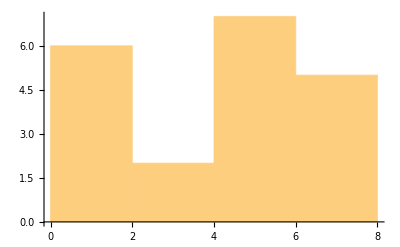

```mathematica
Map[getGeoRange[#,8]&,c]//Histogram
```

## Create the Network

In the last section, we collected the satellite images using GeoImage and store all those images on our hard drive. In this section, we will create our Neural Network so we can feed it with the data we have.

Obtain the all the satellite images’ file name:

```mathematica
trainingFileNames = FileNames["*.png","/Users/mehmetsahin/Downloads/SatelliteImages/Training",Infinity];
testingFileNames = FileNames["*.png","/Users/mehmetsahin/Downloads/SatelliteImages/Testing",Infinity];
ByteCount[trainingFileNames]
ByteCount[testingFileNames]
```

3155680

312488

Define a function to get geo range (zoom level) from the image’s name:

```mathematica
fromFileNameGetGeoRange[fileName_] := 
	ToExpression@First@StringSplit[decodeID[FileBaseName@fileName],"-"];
```

Obtain the training and testing data files:

```mathematica
trainingDataFiles = ParallelMap[File[#]->fromFileNameGetGeoRange[#]&,trainingFileNames];
testingDataFiles = ParallelMap[File[#]->fromFileNameGetGeoRange[#]&,testingFileNames];
```

```mathematica
Import[File@First@trainingFileNames]//ImageDimensions
```

{120,133}

```mathematica
Import[File@"/Users/mehmetsahin/Downloads/SatelliteImages/Testing/ODpBAi1TBVBvaW50wSMBAhOrJ8EVmklA5GSwdV05JEAtUwRab29tch+5Dfr4OGE~/ODpTCDYuMjMzNi03.png"]
```

-Graphics-

```mathematica
n[-Graphics-]
```

0.

```mathematica
testingDataFiles // Dataset;
```

Create a dataset of our training data files so it is easier to visualize:

```mathematica
trainingDataFiles//Dataset;
```

```mathematica
netCNNModel = Take[NetModel["Vanilla CNN for Facial Landmark Regression"],{1,"ActivationAbs4"}]
```

NetChain[<>]

```mathematica
NetModel["Vanilla CNN for Facial Landmark Regression"]
```

NetChain[<>]

Define a convolutional neural network that has an "Image" NetEncoder attached to the input port :

```mathematica
lenet=NetChain[{
ConvolutionLayer[16,5,"PaddingSize"->{2,2}],Tanh,Abs,PoolingLayer[2,2],
ConvolutionLayer[48,3,"PaddingSize"->{1,1}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[64,3,"PaddingSize"->{0,0}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[64,2,"PaddingSize"->{0,0}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[128,2,"PaddingSize"->{0,0}],Tanh,Abs,FlattenLayer[],LinearLayer[1000],Tanh,Abs,LinearLayer[100],Tanh,Abs,LinearLayer[10],SoftmaxLayer[],1},"Output"->"Scalar",
"Input"->NetEncoder[{"Image",{120,133}}]
]
```

NetChain[<>]

```mathematica
trainingDataFiles;
```

```mathematica
testFile = trainingDataFiles[[1,1]]
```

File[/Users/mehmetsahin/Downloads/SatelliteImages/Training/ODpBAi1TBVBvaW50wSMBAg1ka+YXMEhAsVsEvF~ZKEAtUwRab29tcvjjAIjV3so~/ODpTCTE4NDcuNTQtMQ==.png]

```mathematica
NetInitialize[lenet][testFile]
```

-0.103362

Train the net for three training rounds :

```mathematica
trained = NetTrain[lenet,trainingDataFiles,All,ValidationSet->testingDataFiles,MaxTrainingRounds->3]
```

NetTrainResultsObject[<>]

```mathematica
trained["TotalTrainingTime"]
```

1230.54

```mathematica
n = trained["TrainedNet"]
```

NetChain[<>]

```mathematica
n[-Graphics-]
```

0.889465

```mathematica
tempnet = Take[NetModel["VGG-16 Trained on ImageNet Competition Data"], {1, "relu3_1"}]
```

NetChain[<>]

## Test the Network

Now ..

## Conclusion

## Author contact information

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com

## Further Work

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com